Figure 3C:

```mathematica
fibsSanTP17Hi=Import["/Volumes/ahg_regevdata/users/madler/Postdoc/Heart Fibrosis/fibsSanHi_TP17.mat"][[1]];
```

```mathematica
fibsSanTP17HiGenes=Import["/Volumes/ahg_regevdata/users/madler/Postdoc/Heart Fibrosis/fibsSanHiGenes_TP17.txt","Data"][[;;,1]];
```

```mathematica
fibsSanTP17PCA=PrincipalComponents[fibsSanTP17Hi];
```

```mathematica
fibsTP174Arc=Import["/Volumes/ahg_regevdata/users/madler/Postdoc/Heart Fibrosis/fibsTP174Arcs_arc.mat"][[1]];
```

```mathematica
fibsTP174ArcOrig=Import["/Volumes/ahg_regevdata/users/madler/Postdoc/Heart Fibrosis/fibsTP174Arcs_arcOrig.mat"][[1]];
```

```mathematica
fibsTP174ArcErrs=Import["/Volumes/ahg_regevdata/users/madler/Postdoc/Heart Fibrosis/fibsTP174Arcs_errs.mat"][[1,1]];
```

```mathematica
fibsTP174ArcEnrGenes=Import["/Volumes/ahg_regevdata/users/madler/Postdoc/Heart Fibrosis/fibsTP174ArcsGenes_continuous_significant.csv"];
```

```mathematica
fibsTP174ArcEnrGO=Import["/Volumes/ahg_regevdata/users/madler/Postdoc/Heart Fibrosis/fibsTP174ArcsGO_continuous_significant.csv"];
```

```mathematica
Show[{ListPointPlot3D[{-#[[1]],#[[2]],-#[[3]]}&/@fibsSanTP17PCA[[;;500,;;3]],PlotRange->All,PlotStyle->{PointSize[.02],Black}],
ListPointPlot3D[{-#[[1]],#[[2]],-#[[3]]}&/@fibsSanTP17PCA[[501;;,;;3]],PlotRange->All,PlotStyle->{PointSize[.02],Red}],
Graphics3D[{Opacity[0],EdgeForm[Thickness[.005]],ConvexHullMesh[fibsTP174Arc[[{3,4,2,1},;;3]]]}],Graphics3D[{FaceForm[{#[[3]],Opacity[0.5]}],Translate[Rotate[Ellipsoid[{0,0,0},DiagonalMatrix[((*(1/5)*)Eigenvalues[#[[2]]])]],{{1,0,0},Eigenvectors[#[[2]]][[1]]}],#[[1]]]},Boxed->False,BoxRatios->Automatic]}&/@({fibsTP174Arc[[{3,4,2,1},;;3]],fibsTP174ArcErrs[[{3,4,2,1},;;3,;;3]],{Red,Green,Blue,Yellow}}ᵀ),PlotRange->All,Axes->False,BoxRatios->Automatic,Boxed->False]
```

```mathematica
With[{g="F2r"},Show[{Graphics3D[{#[[1]],PointSize[.02],Point[{-#[[1]],#[[2]],-#[[3]]}&@#[[2]]]}&/@({ColorData["DarkRainbow"][#]&/@Rescale[fibsSanTP17Hi[[;;,Position[fibsSanTP17HiGenes,g][[1,1]]]]],fibsSanTP17PCA[[;;,;;3]]}ᵀ)],
Graphics3D[{Opacity[0],EdgeForm[Thickness[.005]],ConvexHullMesh[fibsTP174Arc[[;;,;;3]]]}],Graphics3D[{FaceForm[{#[[3]],Opacity[0.5]}],Translate[Rotate[Ellipsoid[{0,0,0},DiagonalMatrix[((1/6)Eigenvalues[#[[2]]])]],{{1,0,0},Eigenvectors[#[[2]]][[1]]}],#[[1]]]},Boxed->False,BoxRatios->Automatic]}&/@({fibsTP174Arc[[;;,;;3]],fibsTP174ArcErrs[[;;,;;3,;;3]],{Red,Green,Blue,Yellow}}ᵀ),PlotRange->All,Axes->False,BoxRatios->Automatic,Boxed->False,PlotLabel->g]]
```

```mathematica
With[{gene="F2r"},
ticks=Range[Floor[Min[#],.1],Ceiling[Max[#],.1],(Ceiling[Max[#],.1]-Floor[Min[#],.1])/2]&@Table[MeanAround[#][[1]]&/@{#[[;;100,2]],#[[101;;200,2]],#[[201;;300,2]],#[[301;;400,2]],#[[401;;500,2]],#[[501;;600,2]],#[[601;;700,2]],#[[701;;800,2]],#[[801;;900,2]],#[[901;;,2]]}&@SortBy[{EuclideanDistance[fibsTP174ArcOrig[[i]],#[[1]]],#[[2]]}&/@({fibsSanTP17Hi,Rescale[fibsSanTP17Hi[[;;,Position[fibsSanTP17HiGenes,gene][[1,1]]]]]}ᵀ),First],{i,{2,4,3,1}}];
Show[Table[ListLinePlot[MeanAround[#]&/@{#[[;;100,2]],#[[101;;200,2]],#[[201;;300,2]],#[[301;;400,2]],#[[401;;500,2]],#[[501;;600,2]],#[[601;;700,2]],#[[701;;800,2]],#[[801;;900,2]],#[[901;;,2]]}&@SortBy[{EuclideanDistance[fibsTP174ArcOrig[[i]],#[[1]]],#[[2]]}&/@({fibsSanTP17Hi,Rescale[fibsSanTP17Hi[[;;,Position[fibsSanTP17HiGenes,gene][[1,1]]]]]}ᵀ),First],Frame->True,Axes->False,PlotRange->All,FrameTicks->{{{0.15,0.2,0.3}(*ticks*),None},{Automatic,None}},Mesh->Full,PlotStyle->{{Thickness[.005],Red},{Thickness[.005],Green},{Thickness[.005],Blue},{Thickness[.005],Yellow}}[[i]],PlotLabel->Style[gene,20],ImageSize->Small],{i,{1,2,3,4}}],PlotRange->All]]
```

Figure 3D:

```mathematica
macsSanTP17Hi=Import["/Volumes/ahg_regevdata/users/madler/Postdoc/Heart Fibrosis/macsSanHi_TP17.mat"][[1]];
```

```mathematica
macsSanTP17HiGenes=Import["/Volumes/ahg_regevdata/users/madler/Postdoc/Heart Fibrosis/macsSanHiGenes_TP17.txt","Data"][[;;,1]];
```

```mathematica
macsTP174Arc=Import["/Volumes/ahg_regevdata/users/madler/Postdoc/Heart Fibrosis/macsTP174Arcs_arc.mat"][[1]];
```

```mathematica
macsTP174ArcOrig=Import["/Volumes/ahg_regevdata/users/madler/Postdoc/Heart Fibrosis/macsTP174Arcs_arcOrig.mat"][[1]];
```

```mathematica
macsTP174ArcErrs=Import["/Volumes/ahg_regevdata/users/madler/Postdoc/Heart Fibrosis/macsTP174Arcs_errs.mat"][[1,1]];
```

```mathematica
macsTP174ArcEnrGenes=Import["/Volumes/ahg_regevdata/users/madler/Postdoc/Heart Fibrosis/macsTP174ArcsGenes_continuous_significant.csv"];
```

```mathematica
macsTP174ArcEnrGO=Import["/Volumes/ahg_regevdata/users/madler/Postdoc/Heart Fibrosis/macsTP174ArcsGO_continuous_significant.csv"];
```

```mathematica
macsTP174ArcEnrGOAll=Import["/Volumes/ahg_regevdata/users/madler/Postdoc/Heart Fibrosis/macsTP174ArcsGO_continuous_all.csv"];
```

```mathematica
Show[{ListPointPlot3D[{{#[[1]],-#[[2]],#[[3]]}&/@macsSanTP17PCA[[;;323,;;3]],{#[[1]],-#[[2]],#[[3]]}&/@macsSanTP17PCA[[324;;,;;3]]},PlotRange->All,PlotStyle->{{Black,PointSize[.02]},{Red,PointSize[.02]}},BoxRatios->Automatic,Axes->False,Boxed->False],
Graphics3D[{Opacity[0],EdgeForm[Thickness[.005]],ConvexHullMesh[macsTP174Arc[[;;,;;3]]]}],Graphics3D[{FaceForm[{#[[3]],Opacity[0.5]}],Translate[Rotate[Ellipsoid[{0,0,0},DiagonalMatrix[((*(1/5)*)Eigenvalues[#[[2]]])]],{{1,0,0},Eigenvectors[#[[2]]][[1]]}],#[[1]]]},Boxed->False,BoxRatios->Automatic]}&/@({macsTP174Arc[[;;,;;3]],macsTP174ArcErrs[[;;,;;3,;;3]],{Red,Green,Blue,Yellow}}ᵀ),PlotRange->All,Axes->False,BoxRatios->Automatic,Boxed->False]
```

```mathematica
With[{g="Nfkbia"},Show[{Graphics3D[{#[[1]],PointSize[.02],Point[{#[[1]],-#[[2]],#[[3]]}&@#[[2]]]}&/@({ColorData["DarkRainbow"][#]&/@Rescale[macsSanTP17Hi[[;;,Position[macsSanTP17HiGenes,g][[1,1]]]]],macsSanTP17PCA[[;;,;;3]]}ᵀ)],
Graphics3D[{Opacity[0],EdgeForm[Thickness[.005]],ConvexHullMesh[macsTP174Arc[[;;,;;3]]]}],Graphics3D[{FaceForm[{#[[3]],Opacity[0.5]}],Translate[Rotate[Ellipsoid[{0,0,0},DiagonalMatrix[((1/6)Eigenvalues[#[[2]]])]],{{1,0,0},Eigenvectors[#[[2]]][[1]]}],#[[1]]]},Boxed->False,BoxRatios->Automatic]}&/@({macsTP174Arc[[;;,;;3]],macsTP174ArcErrs[[;;,;;3,;;3]],{Red,Green,Blue,Yellow}}ᵀ),PlotRange->All,Axes->False,BoxRatios->Automatic,Boxed->False,PlotLabel->g]]
```

```mathematica
With[{gene="Nfkbia"},
ticks=Range[Floor[Min[#],.1],Ceiling[Max[#],.1],(Ceiling[Max[#],.1]-Floor[Min[#],.1])/2]&@Table[MeanAround[#][[1]]&/@{#[[;;72,2]],#[[73;;144,2]],#[[145;;216,2]],#[[217;;288,2]],#[[289;;360,2]],#[[361;;432,2]],#[[433;;504,2]],#[[505;;576,2]],#[[577;;648,2]],#[[649;;,2]]}&@SortBy[{EuclideanDistance[macsTP174ArcOrig[[i]],#[[1]]],#[[2]]}&/@({macsSanTP17Hi,Rescale[macsSanTP17Hi[[;;,Position[macsSanTP17HiGenes,gene][[1,1]]]]]}ᵀ),First],{i,{2,4,3,1}}];
Show[Table[ListLinePlot[MeanAround[#]&/@{#[[;;72,2]],#[[73;;144,2]],#[[145;;216,2]],#[[217;;288,2]],#[[289;;360,2]],#[[361;;432,2]],#[[433;;504,2]],#[[505;;576,2]],#[[577;;648,2]],#[[649;;,2]]}&@SortBy[{EuclideanDistance[macsTP174ArcOrig[[i]],#[[1]]],#[[2]]}&/@({macsSanTP17Hi,Rescale[macsSanTP17Hi[[;;,Position[macsSanTP17HiGenes,gene][[1,1]]]]]}ᵀ),First],Frame->True,Axes->False,PlotRange->All,FrameTicks->{{{0.3,0.45,0.6}(*ticks*),None},{Automatic,None}},Mesh->Full,PlotStyle->{{Thickness[.005],Red},{Thickness[.005],Green},{Thickness[.005],Blue},{Thickness[.005],Yellow}}[[i]],PlotLabel->Style[gene,20],ImageSize->Small],{i,{1,2,3,4}}],PlotRange->All]]
```

Figure 3G:

```mathematica
arcsCoeffFibs17=Table[Solve[{({-#[[1]],#[[2]],-#[[3]]}&/@fibsSanTP17PCA[[;;,;;3]])[[i,1]]==a #[[1]]+b #[[2]]+c#[[3]]+d#[[4]]&@fibsTP174Arc[[;;,1]],
({-#[[1]],#[[2]],-#[[3]]}&/@fibsSanTP17PCA[[;;,;;3]])[[i,2]]==a #[[1]]+b #[[2]]+c#[[3]]+d#[[4]]&@fibsTP174Arc[[;;,2]],
({-#[[1]],#[[2]],-#[[3]]}&/@fibsSanTP17PCA[[;;,;;3]])[[i,3]]==a #[[1]]+b #[[2]]+c#[[3]]+d#[[4]]&@fibsTP174Arc[[;;,3]],a+b+c+d==1},{a,b,c,d}][[1,;;,2]],{i,1,Length[fibsSanTP17PCA]}];
```

```mathematica
celltimePointsFibs17=Join[ConstantArray[0,500],ConstantArray[28,500]];
```

```mathematica
arcsTask4={{1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,1}};
```

```mathematica
edTaskFibs17=Outer[EuclideanDistance,arcsTask4,arcsCoeffFibs17,1];
```

```mathematica
BoxWhiskerChart[(#[[2]])/(#[[1]])&/@Partition[(Join@@Table[Transpose[Table[N@((#[[2]])/(Length@Select[Transpose[{celltimePointsFibs17,Position[#,Min[#]][[1,1]]&/@Transpose[edTaskFibs17]}][[r]],#[[2]]==i&][[;;,1]]))&/@Table[{d,Count[Select[Transpose[{celltimePointsFibs17,Position[#,Min[#]][[1,1]]&/@Transpose[edTaskFibs17]}][[r]],#[[2]]==i&][[;;,1]],d]},{d,{0,28}}],{r,randInd}]],{i,1,4}]),2]]//Quiet
```

```mathematica
arcsCoeffMacs17=Table[Solve[{({#[[1]],-#[[2]],#[[3]]}&/@macsSanTP17PCA[[;;,;;3]])[[i,1]]==a #[[1]]+b #[[2]]+c#[[3]]+d#[[4]]&@macsTP174Arc[[;;,1]],
({#[[1]],-#[[2]],#[[3]]}&/@macsSanTP17PCA[[;;,;;3]])[[i,2]]==a #[[1]]+b #[[2]]+c#[[3]]+d#[[4]]&@macsTP174Arc[[;;,2]],
({#[[1]],-#[[2]],#[[3]]}&/@macsSanTP17PCA[[;;,;;3]])[[i,3]]==a #[[1]]+b #[[2]]+c#[[3]]+d#[[4]]&@macsTP174Arc[[;;,3]],a+b+c+d==1},{a,b,c,d}][[1,;;,2]],{i,1,Length[macsSanTP17PCA]}];
```

```mathematica
celltimePointsMacs17=Join[ConstantArray[0,323],ConstantArray[28,401]];
```

```mathematica
edTaskMacs17=Outer[EuclideanDistance,arcsTask4,arcsCoeffMacs17,1];
```

```mathematica
BoxWhiskerChart[(#[[2]])/(#[[1]])&/@Partition[(Join@@Table[Transpose[Table[N@((#[[2]])/(Length@Select[Transpose[{celltimePointsMacs17,Position[#,Min[#]][[1,1]]&/@Transpose[edTaskMacs17]}][[r]],#[[2]]==i&][[;;,1]]))&/@Table[{d,Count[Select[Transpose[{celltimePointsMacs17,Position[#,Min[#]][[1,1]]&/@Transpose[edTaskMacs17]}][[r]],#[[2]]==i&][[;;,1]],d]},{d,{0,28}}],{r,randIndMacs}]],{i,1,4}]),2]]//Quiet
```

Figure 4A:

```mathematica
model12[{α21_,β21_,β12_,β11_,μ2_,λ1_,λ2_,x10_,x20_}]:=Module[{adeq,steq},
adeq={
c21[t]+α21 c21[t]/(1+c21[t])x1[t]== β21 x2[t]+β11 x1[t],
c12[t]+c12[t]/(1+c12[t])x2[t]==β12 x1[t],
x1'[t]== x1[t](λ1 c21[t]/(1+c21[t])(1-x1[t])-1) ,
x2'[t]==μ2 x2[t] (λ2 c12[t]/(1+c12[t])-1) };
steq=Equal@@@FindRoot[{c21[0]+(α21 c21[0] x10)/(1+c21[0])==β21 x20+β11 x10,c12[0]+c12[0]/(1+c12[0])x20==β12 x10},{c12[0],1,0,∞},{c21[0],1,0,∞}];
Quiet@NDSolveValue[Join[adeq,steq,{x1[0]==x10,x2[0]==x20}],Norm@{x1[500],x2[500]}<10^-4,{t,0,500}]]
```

```mathematica
HEAL22[x01_?NumericQ,x02_?NumericQ,λ1_,β11_,β12_,β21_]:=Module[{k12=3.6*^9,k21=(*1.3*^9*)1.3*^7,α12=1353600,α21=734400,(*β11=345600,*)(*β12=676800,*)(*β21=100800,*)γ=2,(*λ1=0.9,*)λ2=0.8,μ1=0.3,μ2=0.3},
model12[{(α21 10^6)/(γ k21),β21/k21 k12/α12,(β12 10^6)/(γ k12),(β11 10^6)/(γ k21),μ2/μ1,λ1/μ1,λ2/μ2,10^(x01-6),α12/(k12 γ)10^x02}]]
```

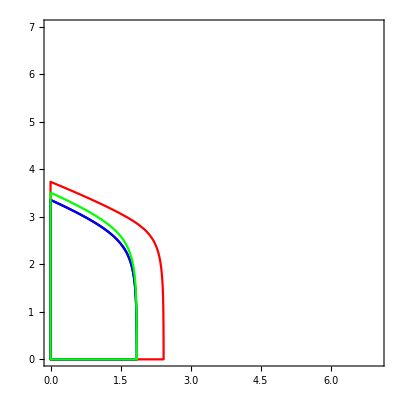

```mathematica
Show[Show[ListLinePlot[
#[[1]][[#[[2,1]]]]&@Cases[RegionPlot[HEAL22[x01,x02,1.2 0.9, 345600,676800,100800],{x01,0,6},{x02,0,8}],{{_Real,_Real}..}|Line[y_],∞],
PlotRange->{{0,7},{0,7}},PlotStyle->Black,AspectRatio->1,Axes->False,Frame->True]],Show[ListLinePlot[
#[[1]][[#[[2,1]]]]&@Cases[RegionPlot[HEAL22[x01,x02,1.2 0.9,0.7 345600,676800,100800],{x01,0,6},{x02,0,8}],{{_Real,_Real}..}|Line[y_],∞],
PlotRange->{{0,7},{0,7}},PlotStyle->Red,AspectRatio->1,Axes->False,Frame->True]],
Show[ListLinePlot[
#[[1]][[#[[2,1]]]]&@Cases[RegionPlot[HEAL22[x01,x02,1.2 0.9,345600,0.7 676800,100800],{x01,0,6},{x02,0,8}],{{_Real,_Real}..}|Line[y_],∞],
PlotRange->{{0,7},{0,7}},PlotStyle->Blue,AspectRatio->1,Axes->False,Frame->True]],
Show[ListLinePlot[
#[[1]][[#[[2,1]]]]&@Cases[RegionPlot[HEAL22[x01,x02,1.2 0.9,345600,676800,0.7 100800],{x01,0,6},{x02,0,8}],{{_Real,_Real}..}|Line[y_],∞],
PlotRange->{{0,7},{0,7}},PlotStyle->Green,AspectRatio->1,Axes->False,Frame->True]]]//Quiet
```

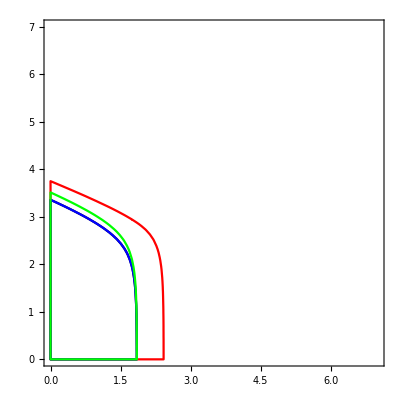

```mathematica
Show[Show[ListLinePlot[
#[[1]][[#[[2,1]]]]&@Cases[RegionPlot[HEAL22[x01,x02,1.2 0.9, 345600,676800/100,100800],{x01,0,6},{x02,0,8}],{{_Real,_Real}..}|Line[y_],∞],
PlotRange->{{0,7},{0,7}},PlotStyle->Black,AspectRatio->1,Axes->False,Frame->True]],Show[ListLinePlot[
#[[1]][[#[[2,1]]]]&@Cases[RegionPlot[HEAL22[x01,x02,1.2 0.9,0.7 345600,676800/100,100800],{x01,0,6},{x02,0,8}],{{_Real,_Real}..}|Line[y_],∞],
PlotRange->{{0,7},{0,7}},PlotStyle->Red,AspectRatio->1,Axes->False,Frame->True]],
Show[ListLinePlot[
#[[1]][[#[[2,1]]]]&@Cases[RegionPlot[HEAL22[x01,x02,1.2 0.9,345600,0.7 676800/100,100800],{x01,0,6},{x02,0,8}],{{_Real,_Real}..}|Line[y_],∞],
PlotRange->{{0,7},{0,7}},PlotStyle->Blue,AspectRatio->1,Axes->False,Frame->True]],
Show[ListLinePlot[
#[[1]][[#[[2,1]]]]&@Cases[RegionPlot[HEAL22[x01,x02,1.2 0.9,345600,676800/100,0.7 100800],{x01,0,6},{x02,0,8}],{{_Real,_Real}..}|Line[y_],∞],
PlotRange->{{0,7},{0,7}},PlotStyle->Green,AspectRatio->1,Axes->False,Frame->True]]]//Quiet
```

Figure 4B:

```mathematica
admodel[{ω_,θ_,α21_,α12_,β12_,β11_,μ2_,λ1_,λ2_,x10_,x20_,I0_,T_,αe_,ϵ_,c_,a_,b_}]:=Module[{adeq,steq},
adeq={
c21[t]+α21 c21[t]/(1+c21[t])x1[t]==(1-1/2 ω (1+ω)+ω c12[t]/(1+c12[t])) x2[t]+β11 x1[t],
c12[t]+α12 c12[t]/(1+c12[t])x2[t]==β12 (1-1/2 θ (1+θ)+θ c21[t]/(1+c21[t])) x1[t],
x1'[t]== x1[t](λ1 c21[t]/(1+c21[t])(1-x1[t])-1) ,
x2'[t]==I0( UnitStep[t]UnitStep[T-t])+μ2 x2[t] (λ2 c12[t]/(1+c12[t])-1),
e'[t]==x1[t]-αe(ϵ+c x2[t])/(a x2[t]+b x1[t]+1)e[t] };
steq=Equal@@@FindRoot[{c21[0]+(α21 c21[0] x10)/(1+c21[0])==(1-1/2 ω (1+ω)+(ω c12[0])/(1+c12[0])) x20+β11 x10,c12[0]+(α12 c12[0])/(1+c12[0])x20==β12 (1-1/2 θ (1+θ)+(θ c21[0])/(1+c21[0])) x10},{c12[0],1,0,∞},{c21[0],1,0,∞}];
Quiet@NDSolveValue[Join[adeq,steq,{x1[0]==x10,x2[0]==x20,e[0]==0}],{x1[t],x2[t],e[t]},{t,0,1000}]]
```

```mathematica
model1[{α21_,α12_,β12_,β11_,μ2_,λ1_,λ2_,x10_,x20_}]:=Module[{adeq,steq},
adeq={
c21[t]+α21 c21[t]/(1+c21[t])x1[t]== x2[t]+β11 x1[t],
c12[t]+α12 c12[t]/(1+c12[t])x2[t]==β12 x1[t],
x1'[t]== x1[t](λ1 c21[t]/(1+c21[t])(1-x1[t])-1) ,
x2'[t]==μ2 x2[t] (λ2 c12[t]/(1+c12[t])-1) };
steq=Equal@@@FindRoot[{c21[0]+(α21 c21[0] x10)/(1+c21[0])==x20+β11 x10,c12[0]+(α12 c12[0])/(1+c12[0])x20==β12 x10},{c12[0],1,0,∞},{c21[0],1,0,∞}];
Quiet@NDSolveValue[Join[adeq,steq,{x1[0]==x10,x2[0]==x20}],Norm@{x1[500],x2[500]}<10^-4,{t,0,500}]]
```

```mathematica
HEAL[x01_?NumericQ,x02_?NumericQ,λ1_,μ1_,α21_,β11_,β12_,k21_]:=Module[{k12=3.6*^9,(*k21=1.3*^9,*)α12=1353600,(*α21=734400,β11=345600,*)(*β12=676800,*)β21=100800,γ=2,(*λ1=0.9,*)λ2=0.8,(*μ1=0.3,*)μ2=0.3},
model1[{(α21 10^6)/(γ k21),(α12 k21)/(β21 k12),(β12 10^6)/(γ k12),(β11 10^6)/(γ k21),μ2/μ1,λ1/μ1,λ2/μ2,10^(x01-6),β21/(k21 γ)10^x02}]]
```

```mathematica
pd2[a_,b_,c_,d_,e_,k12_,k21_]:=Module[{mod,(*k12=3.6*^9,k21=1.3*^9,*)α12=1353600,α21=c 734400,β11=d 345600,β12=676800/e,β21=100800,γ=2,λ1=a 0.9,λ2=0.8,μ1=b 0.3,μ2=0.3},
mod[ic_,α_,I0_,τ_]:=({6,Log10@((β21/(γ k21))^-1)}+Log10@admodel[{0,0,(α 10^6)/(γ k21),(α12 k21)/(β21 k12),(β12 10^6)/(γ k12),(β11 10^6)/(γ k21),μ2/μ1,λ1/μ1,λ2/μ2,10^(-6+ic⟦1⟧),β21/(k21 γ)10^ic⟦2⟧,I0,τ,1,1,1,1,1}][[;;2]]);Quiet@Show[
ParametricPlot[Evaluate@mod[{0.,0.},α21,120,2.1]/.t->0.3 t1,{t1,0,80},PlotRange->{{0,7},{0,7}},PlotStyle->{Black,Dashed}],ListLinePlot[
#[[1]][[#[[2,1]]]]&@Cases[RegionPlot[HEAL[x01,x02,λ1,μ1,α21,β11,β12,k21],{x01,0,6},{x02,0,8}],{{_Real,_Real}..}|Line[y_],∞],
PlotRange->{{0,8},{0,8}},PlotStyle->Black,AspectRatio->1,Axes->False,Frame->True],Graphics[{Arrowheads[Medium],Arrow[BezierCurve[{#,(Evaluate[{6,Log10@((β21/(γ k21))^-1)}+Log10@(admodel[{0,0,(α21 10^6)/(γ k21),(α12 k21)/(β21 k12),(β12 10^6)/(γ k12),(β11 10^6)/(γ k21),μ2/μ1,λ1/μ1,λ2/μ2,10^(#[[1]])/10^6,10^(#[[2]])/(10^(Log10@((β21/(γ k21))^-1))),0,0,1,1,1,1,1}]⟦1;;2⟧)]/.t->0.3),(Evaluate[{6,Log10@((β21/(γ k21))^-1)}+Log10@(admodel[{0,0,(α21 10^6)/(γ k21),(α12 k21)/(β21 k12),(β12 10^6)/(γ k12),(β11 10^6)/(γ k21),μ2/μ1,λ1/μ1,(b λ2)/μ2,10^(#[[1]])/10^6,10^(#[[2]])/(10^(Log10@((β21/(γ k21))^-1))),0,0,1,1,1,1,1}]⟦1;;2⟧)]/.t->0.9),
(Evaluate[{6,Log10@((β21/(γ k21))^-1)}+Log10@(admodel[{0,0,(α21 10^6)/(γ k21),(α12 k21)/(β21 k12),(β12 10^6)/(γ k12),(β11 10^6)/(γ k21),μ2/μ1,λ1/μ1,λ2/μ2,10^(#[[1]])/10^6,10^(#[[2]])/(10^(Log10@((β21/(γ k21))^-1))),0,0,1,1,1,1,1}]⟦1;;2⟧)]/.t->1.2)}]]&/@Flatten[Table[{f0,m0},{f0,{1,3,5,7}},{m0,{1,3,5,7}}],1](*,
Arrow[{{7,0},{6,0}}],Arrow[{{4.3,0},{5,0}}],Arrow[{{3.9,0},{3,0}}],Arrow[{{2,0},{1,0}}],Arrow[{{0,3},{0,2}}],Arrow[{{0,5},{0,4}}]*)}],
ListPlot[FP[{k12,k21,α12,α21,β11,β12,β21,γ,λ1,λ2,μ1,μ2}],PlotStyle->PointSize[.05]],
PlotRange->{{-.5,7},{-.5,7}},AspectRatio->1,Axes->False,Frame->True,FrameLabel->{"Myofibroblasts","Macrophages"}]]
```

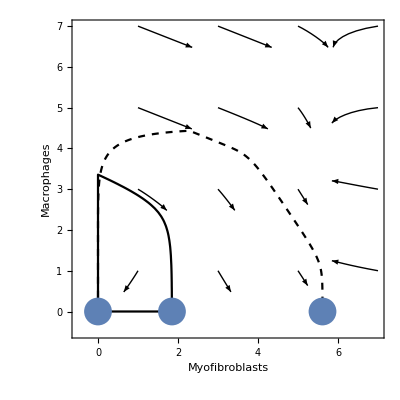
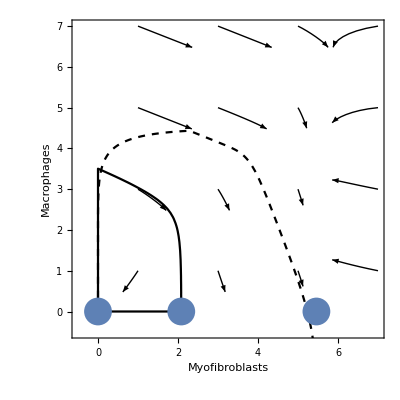
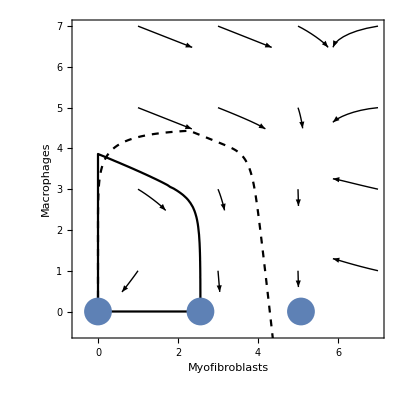
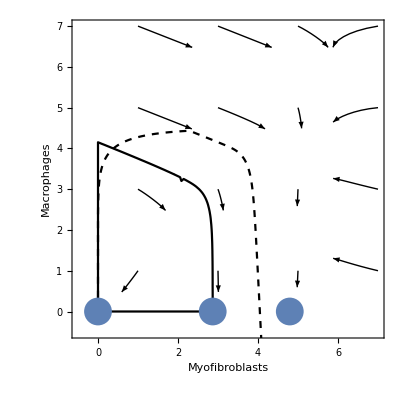
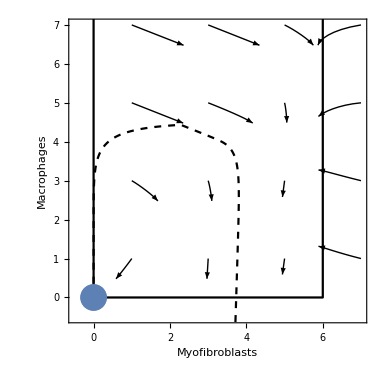
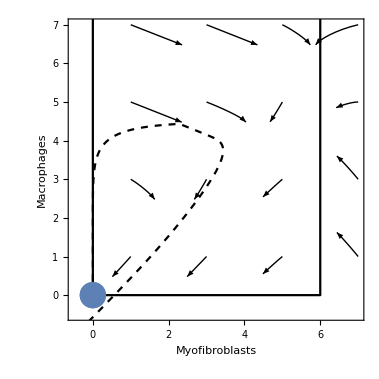

```mathematica
{pd2[1.2,1,1,1,100,3.6*^9,1.3*^7],pd2[1.2,1,1,.83,100,3.6*^9,1.3*^7],pd2[1.2,1,1,.67,100,3.6*^9,1.3*^7],pd2[1.2,1,1,.63,100,3.6*^9,1.3*^7],pd2[1.2,1,1,.58,100,3.6*^9,1.3*^7],pd2[1.2,1,1,.01,100,3.6*^9,1.3*^7]}
```

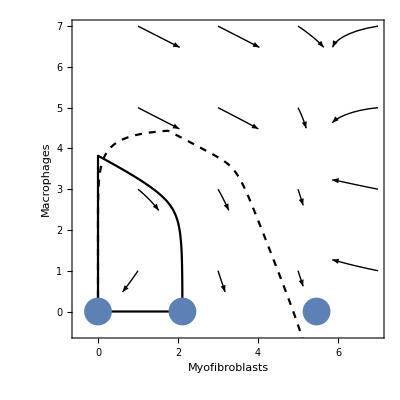
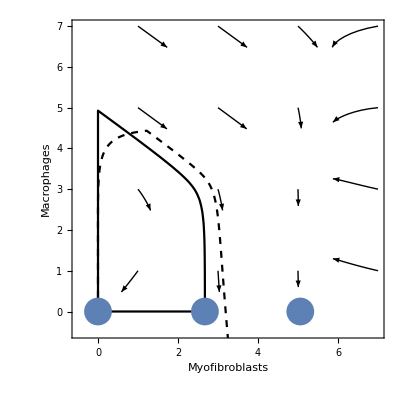
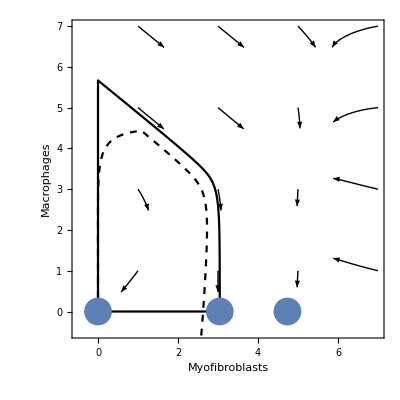
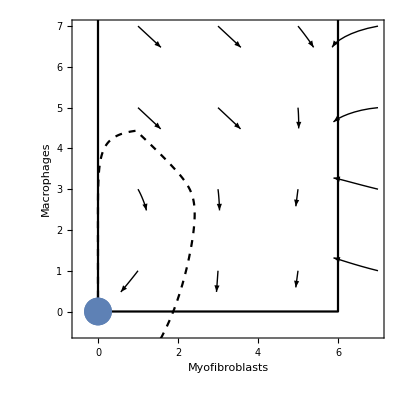
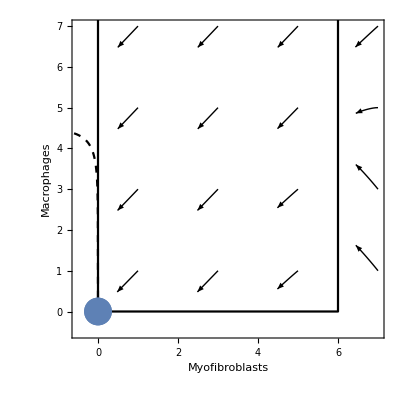
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
{pd2[1.2,1,1,1,100,3.6*^9,1.3*^7],pd2[1,1,1,1,100,3.6*^9,1.3*^7],pd2[.8,1,1,1,100,3.6*^9,1.3*^7],pd2[.75,1,1,1,100,3.6*^9,1.3*^7],pd2[.7,1,1,1,100,3.6*^9,1.3*^7],pd2[.01,1,1,1,100,3.6*^9,1.3*^7]}
```

Figure S4:

myofibroblast proliferating cells:

```mathematica
cellcycleGenes=Import["/Volumes/ahg_regevdata/users/madler/Postdoc/Heart Fibrosis/mouse_cell_cycle_genes.csv"][[2;;,1]];
```

```mathematica
cellcycleGenes//Dimensions
```

{98}

```mathematica
fibsGeneNames=Import["/Volumes/ahg_regevdata/users/madler/Postdoc/Heart Fibrosis/fibsGeneNamesAll.txt","Table"][[;;,1]];
```

```mathematica
fibsGeneNames//Length
```

17202

```mathematica
fibsGeneNames[[Position[fibsGeneNames,Alternatives@@cellcycleGenes][[;;,1]]]]//Length
```

97

```mathematica
fibsDataAll={fibsCellAnnot3,fibsData2}ᵀ;
```

```mathematica
fibsDataAll[[;;,1,1]]//Tally
```

{{9 - Fibro-II,1442},{0 - Fibro-I,11136},{11 - Fibro-III,999},{15 - Fibro-IV,483},{3 - MyoF,3855}}

```mathematica
myoFsAll=Select[fibsDataAll,#[[1,1]]=="3 - MyoF"&];
```

```mathematica
myoFsAll2=GatherBy[myoFsAll,StringSplit[#[[1,2]],"_"][[2]]&];
```

```mathematica
Length/@myoFsAll2
```

{26,8,186,1123,1096,832,584}

```mathematica
prof=Table[Total[#]&/@Normal[myoFsAll2[[i,;;,2]]][[;;,Position[fibsGeneNames,Alternatives@@cellcycleGenes][[;;,1]]]],{i,3,7}];
```

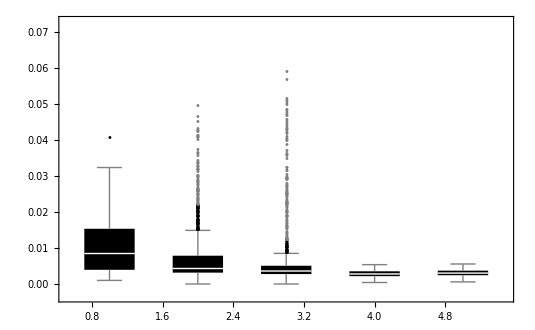

```mathematica
BoxWhiskerChart[prof,"Outliers",ChartStyle->Black,PlotLabel->"Estimated proliferation rate",ChartLabels->{"Day 3","Day 5","Day 7","Day 14","Day 28"}]
```